# Ultrafast dynamics driven by femtosecond lasers in Chern insulators: implementation of semiconductor Bloch equation in topological materials A. Chacon

## Semiconductor Bloch Equations (SBEs) to describe the laser-topological-material interaction

(1)     ∂_t π(k⃗,t) - E⃗(t) ·∇ π(k⃗,t)  = -ⅈ[ϵ_g(  k⃗ )   + (ξ⃗)_g(k⃗) · E⃗(t)  - ⅈ/T2]  π(k⃗,t)   -  ⅈ  (d⃗)_cv(k⃗)  ·  E⃗(t);      Evolution of the coherence,  π(k⃗,t)
     (2)     ∂_t n_c(k⃗,t) - E⃗(t) ·∇ n_c(k⃗,t)  = -2 Im[    Conjugate[ (d⃗)_cv(k⃗)  ]  ·  E⃗(t)  π(k⃗,t) ];                         Evolution of the Occupation, conduction band, nc
     (3)     ∂_t n_v(k⃗,t) - E⃗(t) ·∇ n_v(k⃗,t)  = +2 Im[    Conjugate[ (d⃗)_cv(k⃗)  ]  ·  E⃗(t)  π(k⃗,t) ];                   Evolution of the Occup. of the valence band, nv
       
 Constrain,
        nc(k⃗,t)  + nv(k⃗,t)  =1

```mathematica
ClearAll["Global`*"] ;
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];


rootPathA="/Users/achacon/Documents/Workplace/MichaelC/TopologyProj/CodeDeveloping/March19_2019/";

$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`26"&);
efac=27.2;



toFixedWidth[n_Integer,width_Integer]:=StringJoin[PadLeft[Characters[ToString[n]],width,"0"]];
toNumberedFileName[fname_,n_Integer]:=ToString@StringForm[fname<>toFixedWidth[n,5]]

lfile = "PyAnalysisTMs/laserParam.dat";
mfile = "PyAnalysisTMs/MomGridParam.dat";
bandfile="PyAnalysisTMs/BandsParam.dat";
laserfile="PyAnalysisTMs/outlaserdata.dat";

lfile = rootPathA <> lfile;
mfile = rootPathA <> mfile;
bandfile = rootPathA <> bandfile;
laserfile = rootPathA <> laserfile;
```

## PARAMETERS FOR: Time Axis and more parameters

```mathematica
(* Laser parameters *)
w00=0.014; (*laser freq.*)
e00 = 0.003; (*laser field amplitude*)
Ncycles = 4.; (*No. of cycles*)


T00= 2 Pi/w00; (*laser cycle or period*)

(******* TIME STEP *******)
dt=T00/160.06/2 ;(*Time step*)


alpha0 = Ncycles*T00; (*time width or integration window*)
tmax = 2.0 alpha0;
Ntime = Floor[2 tmax/dt];


olaserParameters ={w00,e00,Ncycles,dt,Ntime};
Export[lfile,olaserParameters,"Data"];


Print["Time-Step dt =",dt,"  a.u."];
Print["Full No. of Time steps, Ntime = ",Ntime];


(*Haldane model parameters*)
t01 =0.075;
t02 = t01/3.0;
M0   =2.54 t02;
phi0 = 1.16; (*0.06*)


T2 = T00; (*Dephasing*)
regular = 10^-20; (*Regularization of Dipole*)
creg = t01/10.; (*Regularization of connection VERY IMPORTANT*)




(*********************************************)
(********* LATTICE CONSTANT a0 ***********)
a0=1./0.529;(*4.5/0.529*)

haldaneparam={a0,t01,t02,M0,phi0,T2};

Export[ bandfile,haldaneparam,"Data"];

(*********************************************)
(* Momentum grid Parameter  *)
dir = 1; (*direction*)
Nsnaper=1;

(*********************************************)




(**************  NUMBERS OF POINTS AT THE BZ *****************)
Nkx= 251;  (*This controls the momentum grid steps*)
Nky =101;
(*yindex=11;*)




(*Creating momentum axis limits*)
xtemp= N[2 Pi/Sqrt[3]/a0];
ytemp= N[2 Pi/3/a0];


kxMin= - xtemp; kxMax=xtemp;
kyMin = - ytemp; kyMax= ytemp; 


dky = 2 kyMax/(Nky-1);


kxMax0 = kxMax; (*Max grid space momentum *)
dktest = 2 kxMax/(Nkx-1);
(*yshift= kyMin +  dky yindex; (**** Momentum on ky-direction ***)
*)

MomParameters ={dktest,Nkx,kxMax,dky,Nky,kyMax};

Export[mfile,MomParameters,"Data"];

Print["\n-------------------------------------\nMomen. grid-step dkx = ",dktest, " a.u."];
Print["Total No. of Momen. Steps, Nkx = ", Nkx];




(***VECTOR BASES OF HM FOR THE HONEYCOMB GRAPHINE TYPE LATTICE ****)


(*Next Nearest Neighbor, NNN, vectors of the HoneyComb Lattice*)
b1 = {Sqrt[3],0}*a0;
b2 = {-Sqrt[3]/2,+3/2}*a0;
b3 = {-Sqrt[3]/2,-3/2}*a0;

b = {b1,b2,b3};

(*Nearest Neighbor, NN, vectors of the HoneyComb Lattice*)
a1 = {0,1}*a0;
a2 = {-Sqrt[3]/2,-1/2}*a0;
a3 = {Sqrt[3]/2,-1/2}*a0;

a= {a1,a2,a3};
aax ={ a1[[1]],a2[[1]],a3[[1]] };
aay ={ a1[[2]],a2[[2]],a3[[2]] };

bbx ={ b1[[1]],b2[[1]],b3[[1]] };
bby ={ b1[[2]],b2[[2]],b3[[2]] };




(*K' and K points with respect to the gamma points on the BZ*)
K1= {-4 Pi/(3*Sqrt[3] a0),0};
K2 = {4 Pi/(3*Sqrt[3] a0),0};
```

Time-Step dt =1.401970981234623283439533  a.u.

Full No. of Time steps, Ntime = 5121

-------------------------------------
Momen. grid-step dkx = 0.0154137 a.u.

Total No. of Momen. Steps, Nkx = 250

Time-Step dt =1.401970981234623283439533  a.u.

Full No. of Time steps, Ntime = 5121

-------------------------------------
Momen. grid-step dkx = 0.0154137 a.u.

Total No. of Momen. Steps, Nkx = 250

Time-Step dt =1.401970981234623283439533  a.u.

Full No. of Time steps, Ntime = 5121

-------------------------------------
Momen. grid-step dkx = 0.0154137 a.u.

Total No. of Momen. Steps, Nkx = 250

Total No. of Momen. Steps, Nkx = 301

## Laser field definition

M/t2 = 2.54;  t2/t1 = 0.3333333333333333333333333;   t1= 2.04 eV; t2= 0.68 eV; M= 1.7272 eV; phi0= 1.16 rad.

Band-Gap= 3.02566;   Max Gap=12.7181 eV

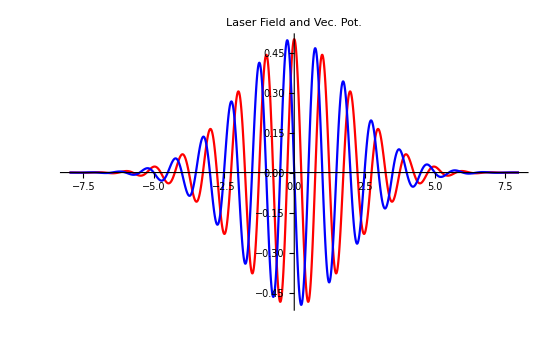

```mathematica
Ef := Function[{t,w0,e0,alpha}, e0 Cos[w0 t] Exp[-2(t/alpha)^2]]; (*we can delete dependence on w0, e0 of Ef*)



timeaxes := Function[
{dt,Nt},

tmax= dt*(Nt-1)/2.;
wmax=Pi/dt;

dw = 2 Pi/Nt/dt;

{Table[-tmax + i dt,{i,0,Nt-1}]
,Table[-wmax + i dw,{i,0,Nt-1}]
}

];



(**DEFINITION OF MOMENTUM AXIS AND OTHERS**)


(* Momentum axis *)
momaxis := Function[
{NkVar,kminVar},

dkVar=Abs[2kminVar/(NkVar-1)];
Table[kminVar + dkVar i,{i,0,NkVar-1}]

]; 


(*Derivative operator on periodic boundary conditions*)
FirstDerOperator := Function [
{dx,Nx},

Mtemp=SparseArray[{Band[{1,1}]->0,Band[{2,1}]->-1,Band[{1,2}]->1},{Nx,Nx}]/2/dx;
Mtemp[[1]][[Nx]]=-1/dx/2;
Mtemp[[1]][[1]]=-0/dx/2;
Mtemp[[Nx]][[Nx]]=0/dx/2;
Mtemp[[Nx]][[1]]=1/dx/2;
Mtemp

];


(*HALDANE MODEL, DIFINITION OF HAMILTONIAN COHEFICIENTS*)

B0 = Function[{kx,ky,t2,ϕ,bx,by}
,2 t2 Cos[ϕ]*
Sum[ 
Cos[ kx *bx[[i]] +ky *by[[i]]  ] 
,{i,1,3}
] 
];


B1= Function[{kx,ky,t1,ax,ay}
, t1 Sum [ 
Cos[ kx *ax[[i]] +ky *ay[[i]] ]
,{i,1,3}
]
];


B2= Function[{kx,ky,t1,ax,ay} 
, t1 Sum[ 
Sin[ kx *ax[[i]] +ky *ay[[i]] ]
,{i,1,3}
]
];


B3= Function[ {kx,ky,t2,M,ϕ,bx,by}
,M-2 t2*Sin[ϕ]Sum[ 
Sin[ kx *bx[[i]] +ky *by[[i]] ]
,{i,1,3} 
] 
];


BNorm=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
, Sqrt[ 
B1[kx,ky,t1,ax,ay]^2 +B2[kx,ky,t1,ax,ay]^2+B3[kx,ky,t2,M,ϕ,bx,by]^2
 ]
];



(*Definition of quantize indexes*)
nB1=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
, B1[kx,ky,t1,ax,ay]/BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] 
];


nB2=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,B2[kx,ky,t1,ax,ay]/BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] 
];


nB3=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
, B3[kx,ky,t2,M,ϕ,bx,by]/BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] 
];


Phi=Function[{kx,ky,t1,t2,M,ϕ,ax,ay}
,ArcTan[ 
B1[kx,ky,t1,ax,ay],
B2[kx,ky,t1,ax,ay] 
]
];

Theta = Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,ArcCos[nB3[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]] 
];



(*GRADIENTS OF B-SETs HAM. Components*)
B0Grad = Function[{kx,ky,t2,ϕ,bx,by}
,Grad[ B0[kkx,kky,t2,ϕ,bx,by]
,{kkx,kky}
]/.kkx-> kx/.kky-> ky 
];

B1Grad = Function[{kx,ky,t1,ax,ay}
,Grad[ B1[kkx,kky,t1,ax,ay]
,{kkx,kky}]/.kkx-> kx/.kky-> ky 
];


B2Grad = Function[{kx,ky,t1,ax,ay}
,Grad[B2[kkx,kky,t1,ax,ay]
,{kkx,kky}]/.kkx-> kx/.kky-> ky 
];


B3Grad = Function[{kx,ky,t2,M,ϕ,bx,by}
,Grad[B3[kkx,kky,t2,M,ϕ,bx,by]
,{kkx,kky}]/.kkx-> kx/.kky-> ky 
];


BNormGrad = Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,Grad[BNorm[kkx,kky,t1,t2,M,ϕ,ax,ay,bx,by]
,{kkx,kky}]/.kkx-> kx/.kky-> ky
];




(*GRADIENTS OF Bloch Sphere angles*)
PhiGrad = Function[{kx,ky,t1,ax,ay,qeps},
(B2Grad[kx,ky,t1,ax,ay] B1[kx,ky,t1,ax,ay] - B1Grad[kx,ky,t1,ax,ay]  B2[kx,ky,t1,ax,ay]) /(B1[kx,ky,t1,ax,ay]^2 + B2[kx,ky,t1,ax,ay]^2+qeps) 
]  ;



ThetaGrad = Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps},-(B3Grad[kx,ky,t2,M,ϕ,bx,by] * BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] - BNormGrad[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] * B3[kx,ky,t2,M,ϕ,bx,by]) /(Sqrt[BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]^2-B3[kx,ky,t2,M,ϕ,bx,by]^2 ]+qeps)/(BNorm [kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] +qeps)
]  ;



(*Definition of Energy dispersion for conduction and valance band*)
Ec=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
, B0[kx,ky,t2,ϕ,bx,by]  + BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]
];



Ev=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
, B0[kx,ky,t2,ϕ,bx,by]  - BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]
];



(*Group velocities of the conduction and valance band*)
cGroupVel = Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,Grad[Ec[kkx,kky,t1,t2,M,ϕ,ax,ay,bx,by],{kkx,kky}]/.kkx-> kx/.kky->ky
];



vGroupVel = Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by},
Grad[Ev[kkx,kky,t1,t2,M,ϕ,ax,ay,bx,by],{kkx,kky}]/.kkx-> kx/.kky->ky
];



(*Definition of the wavefunction for conduction and valance band On BZ*)
uCond=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,
{
Exp[-I*Phi[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]Cos[Theta[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]
,
Exp[I*Phi[kx,ky,t1,t2,M,ϕ,ax,ay]/2]Sin[Theta[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]
}
];



(*'WAVEFUNCTION DEFINITIONS'*)
uVal=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,
{
Exp[-I*Phi[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]Sin[Theta[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]
,
-Exp[I*Phi[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]Cos[Theta[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]/2]
}
];




(*Berry connection and curvature of the conduction band*)
BerryConnectionReg=Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps}
,

1/2 B3[kx,ky,t2,M,ϕ,bx,by] 
/(BNorm[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]+qeps)
PhiGrad[kx,ky,t1,ax,ay,qeps ]  

];




(*Berry curvature of the conduction band*)
cBerryCurvature= Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
,1/2 Cross[ 

Grad[nB3[kkx,kky,t1,t2,M,ϕ,ax,ay,bx,by]
,{kkx,kky,kkz} ]/.kkx-> kx/.kky-> ky

,Grad[Phi[kkx,kky,t1,t2,M,ϕ,ax,ay]
,{kkx,kky,kkz}]/.kkx-> kx/.kky-> ky 
] 
];


cBerryCurvatureNew= Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps}
,
-1/2 Sin[Theta[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by]]
*Cross[ 

{ ThetaGrad[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps][[1]]
,ThetaGrad[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps][[2]]
,0}

, 

{PhiGrad[kx,ky,t1,ax,ay,qeps ][[1]] 
,PhiGrad[kx,ky,t1,ax,ay,qeps ][[2]]
,0}

] 
];


(*Dipole transition matrix element d_cv = i u^*_c d/dk u_v*)
RDipoleCV= Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps}
,1/2 Sin[Theta[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] ]
PhiGrad[kx,ky,t1,ax,ay,qeps] 
]; (*Real part*)



IDipoleCV = Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps}
, 1/2 ThetaGrad[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps]
]; (*Imaginary part*)



Dipole= Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps}
,RDipoleCV[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps]
+I IDipoleCV[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps]
];


CrossDipole:= Function[{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps}
, Abs[
Conjugate[
Dipole[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps][[2]] 
]*
Dipole[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,qeps][[1]]
]
];



(*Energy Gap, Eg = Ec- Ev and Berry Connection 'Chig' Gap*)
 Eg = Function[
{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by}
, Ec[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] 
- Ev[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by] 
];



(*Chig = Chic - Chiv *)
Chig = Function [
{kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,creg}, 
2 BerryConnectionReg[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by,creg]
];






(***BAND GAP****)
(***********************)
(*Max and Min gap*)


dkx1=0.07;
dky1=0.07;

Tac = Table[Ec[kx,ky,t01,t02,M0,phi0,aax,aay,bbx,bby],{kx,kxMin,kxMax,dkx1},{ky,kyMin,kyMax,dky1}];
Tav = Table[Ev[kx,ky,t01,t02,M0,phi0,aax,aay,bbx,bby],{kx,kxMin,kxMax,dkx1},{ky,kyMin,kyMax,dky1}];

Print["M/t2 = ",M0/t02,";  t2/t1 = ",t02/t01, ";   t1= ",t01*efac, " eV; t2= ",t02*efac," eV; M= ",M0*efac," eV; phi0= ",phi0, " rad."]
Print["Band-Gap= ",Min[Tac-Tav]*efac,";   Max Gap=", Max[Tac-Tav]*efac," eV"]






(********************************)
(*Calculation of the CHERN No.*)

CherNo[t1_,t2_,M_,ϕ_,ax_,ay_,bx_,by_]:= -NIntegrate[cBerryCurvature[kx,ky,t1,t2,M,ϕ,ax,ay,bx,by][[3]],{kx,-kxMax,kxMax},{ky,-kyMax, kyMax}  ]/(2 Pi)/2






(*

EVALUATION OF TIME AND MOMENUM AXES 
*)

(*Numerical time axis for time evolution of SBEs*)
tme= timeaxes[dt,Ntime];
time=tme[[]][[1]];
freq = tme[[]][[2]]; 



Plot[Ef[t*T00,w00,e00,alpha0]/w00
,{t,-tmax/T00,tmax/T00}
,PlotRange->All,
PlotStyle->{Red,Blue}
,ImageSize->550
,PlotLabel->"Laser Field and Vec. Pot."]



(*Numerical Momentum Axis creation*)
kxx = momaxis[Nkx,kxMin]; (*momentum space axis*)
dkx = kxx[[2]]-kxx[[1]];(*2 kxMax/(Nkx-1); *)(*Momentum space step => momentum step*)


LaserOut = Table[{j-1,time[[j]],Ef[time[[j]],w00,e00,alpha0]},{j,1,Ntime}];


Export[laserfile,LaserOut,"Data"];

(*Identity matrix and First Derivative operator *)
Id0 = IdentityMatrix[Nkx]; (*Identity matrix*)
DerMatrix = FirstDerOperator[dkx,Nkx]; (*1rst derivative operator*)
















(*Rabbi Freq. *) (*We can obtimize this*)
ROmega := Function[{kx,ky,t}

,Ef[t,w00,e00,alpha0]*
 Dipole[ kx, ky,t01,t02,M0,phi0,aax,aay,bbx,bby, regular][[dir]] 

];












(***************************)
(*
        Loop on ky momentum 
*)

Do[


yshift= kyMin +  dky qindex; (**** Momentum on ky-direction ***)
qindex0=qindex;


(*yshift=0;*)

Print["\n/********************************/\n"];
Print["\nky-index   =    ",yshift, ";        y-index  =  ",qindex, "\n"];


(*Exact Numerical  implementation of the SBEs and ultrafast current oscillations in the topological HM *)


(*Dinamical evolution of populations and SBEs defined by Eqs 1 -- 3, according to the constriction*)
(*SlideView[*)
solver=Function[ky,

NDSolve[

{

(*******************************************)
(****     Evol. Equations of SBEs       ****)
(*******************************************)

(*Equation1*) 
(*We can obtimize it*)

D[pi[kx,t],t] -Ef[t,w00,e00,alpha0]* D[pi[kx,t],kx] == 
-I( Eg[kx,ky,t01,t02,M0,phi0,aax,aay,bbx,bby] 
+Ef[t,w00,e00,alpha0] Chig[kx,ky,t01,t02,M0,phi0,aax,aay,bbx,bby,creg][[dir]]
-  I/T2)* pi[kx,t] 
- I ROmega[kx,ky,t] 


(*Equation2*)
,D[nc[kx,t],t]-Ef[t,w00,e00,alpha0] D[nc[kx,t],kx] == 
-2 Im[ 
Conjugate[ROmega[kx,ky,t]]
* pi[kx,t] 
]

(*******************************************)


(*******************************************)
(****             Initials             ****)
(*******************************************)
(*Initials1*)
,pi[kxMin,t]==pi[kxMax,t]
,pi[kx,-tmax]==0.


(*Initials2*)
,nc[kxMin,t]==nc[kxMax,t]
,nc[kx,-tmax]==0.
(*******************************************)

}

,{pi,nc}

,{kx,kxMin,kxMax}

,{t,-tmax,tmax}

,AccuracyGoal->10,PrecisionGoal->10
(*,Method->"ImplicitRungeKutta",*)
(*,Method-> RK5*)
]

];





(*

Numerical evaluation of Mathematica solutions

*)



mdfun=solver[yshift];

pi0 = Table[
Evaluate[ pi[kxx[[k]],time[[n*Nsnaper]] ]/.mdfun] 
,{n,1,Ntime/Nsnaper},{k,1,Nkx}
];


nc0 = Table[
Re[Evaluate[ nc[kxx[[i]],time[[j*Nsnaper]] ]/.mdfun] ]
,{j,1,Ntime/Nsnaper},{i,1,Nkx}
];


pi1 = Table[
 pi0[[j]][[i]][[1]],
{j,1,Ntime/Nsnaper},{i,1,Nkx}
];


nc1 = Table[
 nc0[[j]][[i]][[1]],
{j,1,Ntime/Nsnaper},{i,1,Nkx}
];

Repi2 = Re[pi1];
ImPi2  =Im[pi1];





(*
Preparing output file names, 
this is one of the time consuming processes,
we can optimize it by outputing in binary files, please,
use BinaryWrite[...,"Real64"], 
*)

fname0 = toNumberedFileName["CoherenceMathRealPiNx_",Nkx];
fname0 = toNumberedFileName[fname0<>"_kyIndex_",qindex0];

fname01 = toNumberedFileName["CoherenceMathImagPiNx_",Nkx];
fname01 = toNumberedFileName[fname01<>"_kyIndex_",qindex0];

fname02 = toNumberedFileName["Integ_Occupation_CMathNx_",Nkx];
fname02 = toNumberedFileName[fname02<>"_kyIndex_",qindex0];

fname03 = toNumberedFileName["Integ_Coherence_ReMathNx_",Nkx];
fname03 = toNumberedFileName[fname03<>"_kyIndex_",qindex0];


fname04 = toNumberedFileName["Integ_Coherence_ImMathNx_",Nkx];
fname04 = toNumberedFileName[fname04<>"_kyIndex_",qindex0];

fname1 = toNumberedFileName["OccupationCBMath_ncNx_",Nkx];
fname1 = toNumberedFileName[fname1<>"_kyIndex_",qindex0];



DataPath0=rootPathA<> fname0<>".dat";
DataPath01= rootPathA<> fname01<>".dat";
(*DataPath02= rootPathA<> fname02<>".dat";
DataPath03= rootPathA<> fname03<>".dat";
DataPath04= rootPathA<> fname04<>".dat";
*)

DataPath1= rootPathA<> fname1<>".dat";



Export[DataPath0,Repi2,"Data"];
Export[DataPath01,ImPi2,"Data"];
Export[DataPath1,nc1,"Data"];

(*Export[DataPath02,integOccupC,"Data"];
Export[DataPath03,integCohRe,"Data"];
Export[DataPath04,integCohIm,"Data"];
*)



,
{qindex,0,101}
]
```

```mathematica
nc1//Dimensions
```

{5121,250}

```mathematica
nc1//Dimensions
(*ListPlot[nc0[[Floor[Nkx/4]]],PlotRange->All,PlotStyle->{Red,Blue},ImageSize->500]*)
```

{5121,250}

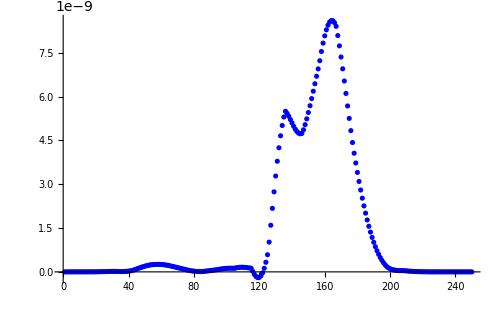

```mathematica
ListPlot[nc1[[]][[130]],PlotRange->All,PlotStyle->{Red,Blue},ImageSize->500]
(*{ListPlot[integOccupC,PlotRange->All,PlotStyle->{Red,Blue},ImageSize->500]
,ListPlot[{integCohIm,integCohRe},PlotRange->All,PlotStyle->{Red,Blue},ImageSize->500,Joined->True]}
*)
```

```mathematica
Visualization of the SBEs via Mathematica Solvers
```

Mathematica of SBEs Solvers the via Visualization

```mathematica
(*
downky =.0;
upky     = .0;
stepky=.1;


mdfun=solver[yshift];

(*Dinamical evolution of populations and SBEs*)
(*SlideView[*)
(*Table[
mdfun=solver[yshift];
*)

{Plot[
Eg[kx,yshift,t01,t02,M0,phi0,aax,aay,bbx,bby] 
,{kx,kxMin,kxMax}
,PlotRange-> {All,{0,All}},
PlotLabel->"Eg"
,ImageSize->350 
,PlotStyle->Gray
],

ImxyDip= Table[{kx,Im[ROmega[kx,yshift,0] ]},{kx,kxMin,kxMax,0.025}];

ListPlot[ImxyDip
, PlotStyle-> Blue
, PlotLegends-> Automatic
,PlotRange->All
,ImageSize->350
,PlotLabel-> {"Dipole, ky = ", yshift}
],

ImxyDip= Table[{kx,Chig[kx,yshift,t01,t02,M0,phi0,aax,aay,bbx,bby,creg][[dir]]},{kx,kxMin,kxMax,0.025}];

ListPlot[ImxyDip
, PlotStyle-> Red
, PlotLegends-> Automatic
,PlotRange->All
,ImageSize->350
,PlotLabel-> "BConnection"
]

,

(*DensityPlot[
Im[Evaluate[pi[kx,t]/.mdfun]]
,{kx,kxMin,+kxMax}
,{t,-tmax,tmax}
(*,Frame -> True*)
(*,FrameLabel-> Automatic*)
,ColorFunction->"GrayYellowTones"
,PlotPoints-> 200
,PlotRange->All
,ImageSize->300
,PlotLabel-> "Coherence"
, PlotLegends-> Automatic
 ]
,*)
ListDensityPlot[
pi1
,Mesh->None
,PlotRange -> All
,ColorFunction->"GrayYellowTones"
,PlotLabel-> "Evol. of the phi: Mathematica"
,ImageSize->300
,PlotLegends-> Automatic
,PlotRangePadding->None 
, InterpolationOrder-> 2
,Frame->True
,FrameLabel-> Automatic
]

,
(*DensityPlot[
Re[ Evaluate[nc[kx,t]/.mdfun] ]
,{kx,kxMin,+kxMax}
,{t,-tmax,tmax}
,Frame -> True
,FrameLabel-> Automatic
,ColorFunction->"GrayYellowTones"
,PlotPoints-> 150
,PlotRange->All
,ImageSize->300
,PlotLabel-> "Populations"
, PlotLegends-> Automatic
]*)
ListDensityPlot[
nc1
,Mesh->None
,PlotRange -> All
,ColorFunction->"GrayYellowTones"
,PlotLabel-> "Evol. of the nc: Mathematica"
,ImageSize->300
,PlotLegends-> Automatic
,PlotRangePadding->None 
, InterpolationOrder-> 2
,Frame->True
,FrameLabel-> Automatic
]
,

picut=Partition[Flatten[Table[{kx,Re[Evaluate[pi[kx,0]/.mdfun]]},{kx,kxMin,kxMax,.02}]],2];

ListPlot[
picut
, PlotStyle-> Blue
, PlotLegends-> Automatic
,PlotRange->All
,ImageSize->300
,PlotLabel-> {"Coherence at t=0 and ky = ", yshift}
]
}
(*,
{yshift,downky,upky,stepky}
]*)


*)
```

## Evaluation of experimental observable or exact observables

#### Inter-dipole and radiation

```mathematica
(*(*************************************************
x-direction analysis for the inter-band current
   ****)


DtimeOp = FirstDerOperator[dt,Ntime];

xInterRad0 = Table[

xInterDipole[kxx[[i]],yshift,time[[j]],mdfun] 

,{i,1,Nkx} 
,{j,1,Ntime}

];


(*Momentum expectation value of the dipole moment on x-direction*)
xDipoleMom = Table[
 
Sum[

xInterRad0[[i]][[j]][[1]]*dkx
,{i,1,Nkx}

]

,{j,1,Ntime}

];

(******************************)
(*x-Interband Current*)
xInterRad=DtimeOp.xDipoleMom;
(******************************)


(*************************************************
y-direction analysis for the inter-band current
    ****)
yInterRad0 = Table[

yInterDipole[kxx[[i]],yshift,time[[j]],mdfun] 

,{i,1,Nkx} 
,{j,1,Ntime}

];


(*Momentum expectation value of the dipole moment on y-direction*)
yDipoleMom = Table[ 

Sum[

yInterRad0[[i]][[j]][[1]]*dkx
,{i,1,Nkx}

]

,{j,1,Ntime}

];


(******************************)
(*y-Interband Current*)
yInterRad=DtimeOp.yDipoleMom;
(******************************)




*)
```

#### Intraband analysis

```mathematica
(*
(*************************************************
x-direction analysis for the intra-band current
   ****)
xIntraRad0 = Table[

xgroupVelocity[kxx[[i]],yshift,time[[j]],mdfun] 

,{i,1,Nkx} 
,{j,1,Ntime}

];

(*Momentum expectation value of the intra-band momentum dependent on x-direction*)
xIntraRad = Table[
 
Sum[

xIntraRad0[[i]][[j]][[1]]*dkx
,{i,1,Nkx}

]

,{j,1,Ntime}

];


(*************************************************
y-direction analysis for the intra-band current
   ****)
yIntraRad0 = Table[

ygroupVelocity[kxx[[i]],yshift,time[[j]],mdfun] - yanomalousVelocity[kxx[[i]],yshift,time[[j]],mdfun]

,{i,1,Nkx} 
,{j,1,Ntime}

];


(*Momentum expectation value of the intra-band momentum dependent on y-direction*)
yIntraRad = Table[
 
Sum[

yIntraRad0[[i]][[j]][[1]]*dkx
,{i,1,Nkx}

]

,{j,1,Ntime}

];*)
```

```mathematica
(*{ ListPlot[{xIntraRad,yIntraRad},Joined->True,PlotRange->All,PlotStyle->{Blue,Red},PlotLabel->"Exact-Mathematica Sol.: Blue x-intra,    Red y-intra",ImageSize->450],
ListPlot[{xInterRad,yInterRad},Joined->True,PlotRange->All,PlotStyle->{Blue,Red},PlotLabel->"Exact-Mathematica Sol.: Blue x-inter,    Red y-inter",ImageSize->450]}
*)
```

## Inter-band Currents Comparison Mathematica vs Crank-Nicholson Solvers

```mathematica
(*
ListPlot[{xInterRad, xinter0},PlotRange->{All,All}, Joined->{True,True},PlotStyle->{Red,Blue},PlotLabel->"Red. Interband Exact Math. -- Blue. Numerical Crank-Nicholson"]*)
```

## HHG Spectra visualizations

```mathematica
(*

vec = Log10[Abs[ Fourier[ xinter0]  ]^2+ 10^-15];
vec=RotateRight[vec,Quotient[Length[vec],2]];

evec = Log10[Abs[ Fourier[xInterRad]  ]^2+ 10^-15];
evec=RotateRight[evec,Quotient[Length[evec],2]];

dt = tmax*2/Ntime;
wmax= Pi/dt;
dw = 2 Pi/Ntime/dt;

spectrum = Table[{(-wmax+dw i)/w00,vec[[i+1]]},{i,0,Ntime-1}];
espectrum = Table[{(-wmax+dw i)/w00,evec[[i+1]]},{i,0,Ntime-1}];

{ListPlot[{xInterRad,xinter0}
,PlotRange->{All,All}
,ImageSize->450
,  Joined->True
,PlotLabel->{"Interband Currents at ky =", yshift}
,PlotStyle->{Red,Blue}
]
,
ListPlot[{spectrum ,espectrum}
,ImageSize->450,Joined->True 
,PlotRange->{{0,37},{-15,Max[vec]}}
,PlotStyle->{Blue,Red}
,PlotLabel->"Red. Interband Exact Math. Sol. -- Blue. Numerical Crank-Nicholson Sol."

]} 


*)
```